```mathematica
DD[ k_, a_, n_ ] := Sum[(-1)^(j+1) Binomial[k,j] DD[ k-j, m, Floor[n/(m^j)]], {m,a, n^(1/k)},{j,1,k}]
DD[ 1,a_, n_ ]:= Floor[n]-a+1
DD[0,a_,n_] := 1
DS[ n_, k_ ] := DD[k,2,n]
DDD[n_, k_ ] := Sum[ DDD[n/j, k-1],{j,2,n}]
DDD[n_,0] := 1
```

```mathematica
DS[1000,2]
```

5070

```mathematica
DDD[1000,2]
```

5070

```mathematica
DS[n,1]
```

-1+Floor[n]

```mathematica
D2[n_] := Sum[ Binomial[2,1](Floor[n/m]-m+1) -Binomial[2,0],{m,2,Floor[n^(1/2)]}]
```

```mathematica
D2[n]
```

```mathematica
D3[n_]:=∑_(m=2)^Floor[√n] (-1+2 (1-m+Floor[n/m]))
```

```mathematica
Expand[-1+2 (1-m+Floor[n/m])]
```

1-2 m+2 Floor[n/m]

```mathematica
∑_(m=2)^Floor[√n] (1-2 m+2 Floor[n/m])
```

```mathematica
∑_(m=2)^Floor[√n] (1-2 m+2 Floor[n/m])
```

```mathematica
∑_(m=2)^Floor[√n] 1+∑_(m=2)^Floor[√n] -2 m+∑_(m=2)^Floor[√n] 2 Floor[n/m]
```

1-Floor[√n]^2+∑_(m=2)^Floor[√n] 2 Floor[n/m]

```mathematica
D3a[n_]:=∑_(m=2)^Floor[√n] (1-2 m+2 Floor[n/m])
```

```mathematica
D3[n_]:=∑_(m=2)^Floor[√n] 1 +∑_(m=2)^Floor[√n] -2 m+∑_(m=2)^Floor[√n] (2 Floor[n/m])
```

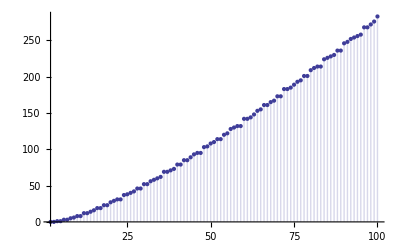

```mathematica
DiscretePlot[D3[n],{n,2,100}]
```

```mathematica
D3[1000]
```

5070

```mathematica
FullSimplify[ ∑_(m=2)^Floor[√n] 1 +∑_(m=2)^Floor[√n] -2 m+∑_(m=2)^Floor[√n] (2 Floor[n/m]) ]
```

1-Floor[√n]^2+∑_(m=2)^Floor[√n] 2 Floor[n/m]

```mathematica
D4[n_] := 1-Floor[√n]^2+2∑_(m=2)^Floor[√n] Floor[n/m]
```

```mathematica
DiscretePlot[D4[n],{n,2,100}]
```

-Graphics-

```mathematica
D4[1000]
```

5070